```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[x_, y_]]
```

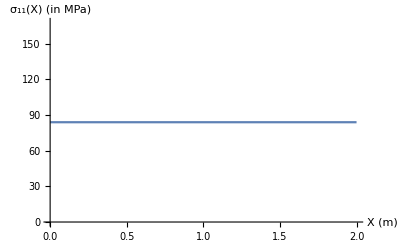

```mathematica
L=2; (*in m*)
α=12 10^-6; (*1/degree centigrade*)
Ε=1.0 10^11; (*in Pa*)
ΔT=80-10; (*in degree centigrade*)
δ=α ΔT L//N;
Subscript[σ, 11][X_]:=α ΔT Ε
Plot[Subscript[σ, 11][X]/10^6,{X,0,L},AxesLabel->{"X (m)","σ_11(X) (in MPa)"}]
```